# Computations for Greenbaum et al.

## Generating vector field plots with basins of attraction (Fig. 2, S14)

```mathematica
$HistoryLength=0;

dynamics[q10_,q20_,ss_,cc_,hh_,mm_,time_]:=Module[{q1,q2,list1,list2,q1t,q2t},(*two lists of the dynamics, for q1 and q2, given starting conditions, up to time*)
q1=q10;q2=q20;
list1={q1};list2={q2};
Do[
q1t=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q1+mm q2};
q2t=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q2+mm q1};
q1=q1t;q2=q2t;
AppendTo[list1,q1];
AppendTo[list2,q2];
,time];
{list1,list2}
]
eqpoints[ss_,cc_,hh_,mm_]:=Module[{q1,q2,eeq1,eeq2,sols,z1,z2,z3,sn,sc},(*Gives the equilibrium solutions for s,c,h,m*)
eeq1=q1==(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q1+mm q2};
eeq2=q2==(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q2+mm q1};
sols=Quiet[NSolve[{eeq1,eeq2},{q1,q2},Reals]];
If[Length[sols]==7,sols=Quiet[Solve[{eeq1,eeq2},{q1,q2},Reals]]];
z1=Table[
If[
Length[sss]≠2,"N",
If[sss⟦1,2⟧<0-10^-5||sss⟦2,2⟧<0-10^-5||sss⟦1,2⟧>1.+10^-5||sss⟦2,2⟧>1.+10^-5,"N",{sss⟦1,2⟧,sss⟦2,2⟧}]
](*Here we remove all solution that are not in the interval [0,1] with some small error margin due to numeric accuracy*)
,{sss,sols}];
z2=DeleteCases[z1,"N"];
z3=DeleteDuplicates[Round[z2,10^-5]];(*Due to numeric accuracy, some solutions are counted twice sometimes. Here we remove duplicate solutions*)
N[Sort[z3]]
]

attractor[q10_,q20_,s_,c_,h_,m_,time_,th_,attarctors_]:=Module[{dd,dd1,distances,a1},(*Given a list of attractors, for a point (q10,q20) returns the closest attractor after dynamics run for time, as long as it is within distance th. otherwise, returns 0*)
dd=dynamics[q10,q20,s,c,h,m,time];
dd1={Last[dd⟦1⟧],Last[dd⟦2⟧]};
distances=Table[EuclideanDistance[dd1,a],{a,attarctors}];
a1=Position[distances,Min[distances]]⟦1,1⟧;
If[distances⟦a1⟧<th,a1,0]
]


cff[x_]:=If[x==0,White,Lighter[colors⟦x⟧,0.4]]
(*Color function for attraction basin plot*)

PlotAttraction[ss_,cc_,hh_,mm_,th_,time_]:=Module[{},(*Plots a 101*101 array for q1*q2 of the equilibria and attarction basins*)
eqs=eqpoints[ss,cc,hh,mm];
txx=ParallelTable[attractor[q1,q2,ss,cc,hh,mm,time,th,eqs],{q1,0,1,0.01},{q2,0,1,0.01}];
colors1=ColorData[97,"ColorList"];
colors=ReplacePart[colors1,{7->colors1⟦8⟧,8->colors1⟦7⟧,5->colors1⟦6⟧,6->colors1⟦5⟧}];
colors=AppendTo[colors⟦1;;Length[eqs]-1⟧,Red];
l0=ListPlot[{{0,0.5}},Frame->{{True,False},{True,False}},FrameTicks->{{{0,0,{0,0}},{0.25,"",{0.03,0.03}},{0.5,0.5,{0.03,0.03}},{0.75,"",{0.03,0.03}},{1,1,{0.03,0.03}}},{{0,0,{0,0}},{0.25,"",{0.03,0.03}},{0.5,0.5,{0.03,0.03}},{0.75,"",{0.03,0.03}},{1,1,{0.03,0.03}}}},PlotRange->{{0,1},{0,1}},AxesOrigin->{0,0},AspectRatio->1,FrameTicksStyle->Directive[Black,35],PlotRangeClipping->False,PlotRangePadding->0.03,FrameStyle->White];
l1=ListPlot[Partition[eqs,1],PlotMarkers->Table[Graphics[{EdgeForm[{Black,Thin}],FaceForm[ccc],Disk[]},ImageSize->15],{ccc,colors}],Frame->{{True,False},{True,False}},FrameTicks->{{0,0.5,1},{0,0.5,1}},AspectRatio->1,PlotRangeClipping->False];
l2=MatrixPlot[Transpose[txx],ColorFunction->cff,ColorFunctionScaling->False,FrameTicks->{{0,0.5,1},{0,0.5,1}},DataRange->{{0,1},{0,1}},DataReversed->True];
a1=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q1+mm q2};
a2=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q2+mm q1};
l3=VectorPlot[{a1-q1,a2-q2},{q1,0,1},{q2,0,1},VectorStyle->Darker[Gray],VectorPoints->Automatic];
l3=Show[l0,l2,l3,l1]
]
```

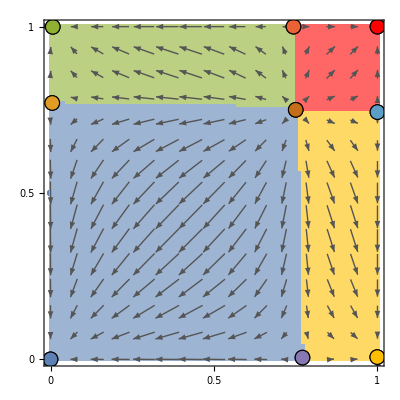

```mathematica
s=0.8;c=1;h=1;
m=0.01;
DateString[]
res=PlotAttraction[s,c,h,m,0.01,100]
DateString[]
```

## Computing m^* and q_2^* (Fig. 3, S2)

```mathematica
$HistoryLength=0;
DTEvalid[cc_,hh_,ss_,mm_]:=Module[{y1,y2,out,qnext1,qnext2,q,sn,sc,q1,q2,eqSolutions,eqSolutions2,outq2,rr2,rr3,rr4,rr5,rr6},(*For a given c,h,s, and m, tests if a DTE exists*)
out=1;outq2="Na";
If[ss==0,out=0,
qnext1=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q1+mm q2};(*Eq. 3*)
qnext2=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q2+mm q1};(*Eq. 3*)
(*Next 4 code lines switch from Eq.3 to Eq. S2. Activate these lines for generating Fig. S2 (selection before migration)*)
(*qnext1a=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1- ss),q->q1};
qnext2b=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1- ss),q->q2};
qnext1=((1-aa mm)qnext1a+mm qnext2b)/(1-aa mm+mm);
qnext2=((1-mm )qnext2b+aa mm qnext1a)/(1+aa mm-mm);*)
eqSolutions=Quiet[NSolve[qnext1==q1&&qnext2==q2,{q1,q2}]];(*Finding equilibrium solutions for Eq. 3*)
eqSolutions2=N[Round[Table[{e⟦1,2⟧,e⟦2,2⟧},{e,eqSolutions}],10^-3]];
If[Union[Flatten[Table[{Im[e⟦1⟧],Im[e⟦2⟧]},{e,eqSolutions2}]]]≠{0},out=0];(*Checks that all solutions are real*)
y2=If[out==1,Union[Table[If[0≤t≤1,1,0],{t,Flatten[eqSolutions2]}]]];(*Checks that all solutions are between 0 and 1*)
If[y2≠{1},out=0];
If[out==1,(*Compute Subscript[q, 2] of the DTE*)
jacobian={{D[qnext1,q1],D[qnext1,q2]},{D[qnext2,q1],D[qnext2,q2]}}; (*The Jacobian from equation 5.*)
rr2=Table[Abs[Eigenvalues[jacobian/.{r⟦1⟧,r⟦2⟧}]],{r,eqSolutions}]; (*Taking the absolute eigenvalues for the jacobian evaluated at the different solutions*)
rr3=Table[If[e⟦1⟧<1&&e⟦2⟧<1,True,False],{e,rr2}];(*Testing to see for each equilibrium point if it is stable*)
rr4=Round[Table[{e⟦1,2⟧,e⟦2,2⟧},{e,eqSolutions}],0.00001];
rr5=Table[If[rr3⟦i⟧&&(rr4⟦i,1⟧>rr4⟦i,2⟧),rr4⟦i,2⟧,Null],{i,Length[eqSolutions]}]; (*Taking all the points that are stable and Subscript[q, 1]>Subscript[q, 2]*)
rr6=DeleteCases[rr5,Null];
If[rr6=={},out=0];(*If there are no DTEs, out=0*)
outq2=If[Length[rr6]==1,rr6⟦1⟧,Null] (*Making sure that there is only one DTE, and taking Subscript[q, 2] of the DTE*)
];
];
{out,outq2}(*out=1 means DTE exists, otherwise out=0*)
]

mqstar[cc_,hh_,ss_]:=Module[{maxm,jumps,t0,t1,t2,t3,outm,w1,outq}, (*For a given c, h, and s, returns m^* and Subscript[q, 2]^* *)
If[DTEvalid[cc,hh,ss,0]⟦1⟧==0,outm="Na";outq="Na",
maxm=0.13;(*Maximal m for searching m^* *)
jumps=10^-3;(*Resolution in m for searching m^*  *)
t0=Table[{N[mm],DTEvalid[cc,hh,ss,mm]},{mm,0,maxm,jumps}];
t1=Table[{t⟦1⟧,t⟦2,1⟧},{t,t0}];
t2=Flatten[Take[t1,All,{2}]];
t3=Flatten[t1⟦FirstPosition[t2,0]-1⟧]⟦1⟧;
outm=If[NumberQ[t3],t3,"Na"];
w1=Table[{t⟦1⟧,t⟦2,2⟧},{t,t0}];
outq=Max[DeleteCases[Flatten[Take[w1,All,{2}]],"Na"]]
];
{outm,outq}
]

ComputeGridmqstar[h_]:=Module[{jmps,jmpc,ress,pmstar,pqstar},
jmps=0.01;(*resolution in s*)
jmpc=0.01;(*resolution in c*)
ress=Quiet[ParallelTable[Table[{ccc,sss,mqstar[ccc,h,sss]},{ccc,0,1,jmpc}],{sss,0,1,jmps}]];
pmstar=Table[{r⟦1⟧,r⟦2⟧,r⟦3,1⟧},{r,Flatten[ress,1]}];
pqstar=Table[{r⟦1⟧,r⟦2⟧,r⟦3,2⟧},{r,Flatten[ress,1]}];
{pmstar,pqstar}
]
```

```mathematica
h=0;
p1=ComputeGridmqstar[h];
```

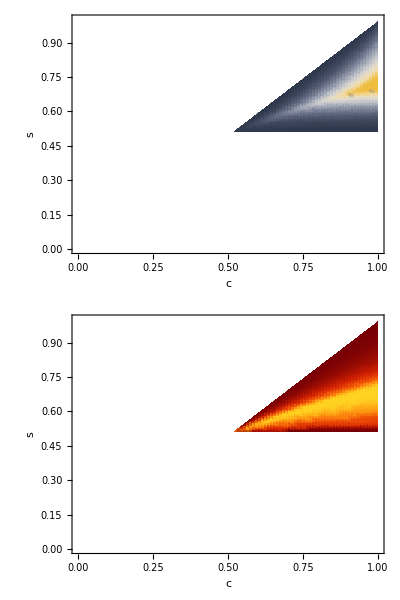

```mathematica
cf1[x_]:=If[!NumberQ[x],White,ColorData["GrayYellowTones"][x/0.075]]
cf2[x_]:=If[!NumberQ[x],White,ColorData["SolarColors"][x/0.22]]
gm1=ListDensityPlot[p1⟦1⟧,PlotRange->{{0,1},{0,1},{0,0.3}},ColorFunction->cf1,ColorFunctionScaling->False,FrameLabel->{"c","s"},FrameTicksStyle->10];
gq1=ListDensityPlot[p1⟦2⟧,PlotRange->{{0,1},{0,1},{0,0.3}},ColorFunction->cf2,ColorFunctionScaling->False,FrameLabel->{"c","s"},FrameTicksStyle->10];
Grid[{{gm1},{gq1}}]
```

## Computing trajectories of q* with incase in m (Fig. 4)

```mathematica
eqpointsMbS[ss_,cc_,hh_,mm_]:=Module[{q1,q2,eeq1,eeq2,sols,z1,z2,z3},(*Gives the equilibrium solutions for s,c,h,m*)
eeq1=q1==(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q1+mm q2};
eeq2=q2==(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q2+mm q1};
sols=Quiet[NSolve[{eeq1,eeq2},{q1,q2},Reals]];
z1=Table[
If[
Length[ss]≠2,"N",
If[ss⟦1,2⟧<0-10^-5||ss⟦2,2⟧<0-10^-5||ss⟦1,2⟧>1.+10^-5||ss⟦2,2⟧>1.+10^-5,"N",{ss⟦1,2⟧,ss⟦2,2⟧}]
](*Here we remove all solution that are not in the interval [0,1] with some small error margin due to numeric accuracy*)
,{ss,sols}];
z2=DeleteCases[z1,"N"];
z3=DeleteDuplicates[Round[z2,10^-5]];(*Due to numeric accuracy, some solutions are counted twice sometimes. Here we remove duplicate solutions*)
N[Sort[z3]]
]

dynamicsMbS[q10_,q20_,ss_,cc_,hh_,mm_,time_]:=Module[{q1,q2,list1,list2,q1t,q2t},(*two lists of the dynamics, for q1 and q2, given starting conditions, up to time*)
q1=q10;q2=q20;
list1={q1};list2={q2};
Do[
q1t=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q1+mm q2};
q2t=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q2+mm q1};
q1=q1t;q2=q2t;
AppendTo[list1,q1];
AppendTo[list2,q2];
,time];
{list1,list2}
]

attractorMbS[q10_,q20_,s_,c_,h_,m_,time_,th_,attarctors_]:=Module[{},(*Given a list of attractors, for a point (q10,q20) returns the closest attractor after dynamics run for time, as long as it is within distance th. otherwise, returns 0*)
dd=dynamicsMbS[q10,q20,s,c,h,m,time];
dd1={Last[dd⟦1⟧],Last[dd⟦2⟧]};
distances=Table[EuclideanDistance[dd1,a],{a,attarctors}];
a1=Position[distances,Min[distances]]⟦1,1⟧;
If[distances⟦a1⟧<th,a1,0]
]


mplusepsilonMbS[s_,c_,h_]:=Module[{},
epsilon=0.005;
mst=mqstar[c,h,s]⟦1⟧;
atr=eqpointsMbS[s,c,h,mst+epsilon];
qq=qMbS[s,c,h,mst];
time=1000;
thr=0.1;
pp=attractorMbS[qq⟦1⟧,qq⟦2⟧,s,c,h,mst+epsilon,time,thr,atr];
atr⟦pp⟧
]

qeqtrajMbS[s_,c_,h_]:=Module[{},
ms=mqstar[c,h,s]⟦1⟧;
tt=ParallelTable[qMbS[s,c,h,m],{m,0,ms,0.001}];
ee=mplusepsilonMbS[s,c,h];
{tt,ee}
]


plottraj1[list_,color_]:=Module[{},
templist=DeleteCases[list⟦2,1⟧,"N2"];
dd1=ListPlot[templist,Joined->True,PlotStyle->Directive[color,Arrowheads[20]],PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->{{0,0.2,0.4,0.6,0.8,1},{0,0.2,0.4,0.6,0.8,1}},AspectRatio->1,FrameTicksStyle->18] /.Line[x_]:>{Arrowheads[{0,0,0,0,If[MemberQ[{0.719},list⟦1⟧],0.05,0],0,If[MemberQ[{0.7,0.75,0.8},list⟦1⟧],0.05,0]}],Arrow[x]};
dd2=ListPlot[{Last[templist],list⟦2,2⟧},Joined->True,PlotStyle->{Dashed,color}]/.Line[x_]:>{Arrowheads[{0,0,If[MemberQ[{0.7,0.719,0.72,0.75,0.8},list⟦1⟧],0.05,0],0,0,0,0,0,0}],Arrow[x]};
Show[dd1,dd2]
]
```

```mathematica
c=1;h=0;
```

```mathematica
svalues={0.55,0.6,0.65,0.7,0.719,0.720,0.75,0.8,0.85,0.89};
DateString[]
wa1=Table[{s,qeqtrajMbS[s,c,h]},{s,svalues}];
DateString[]
```

```mathematica
cf1[s_,smax_]:=If[s≥smax,Darker[Blue,1-((s-smax)/(1-smax))^0.3],Darker[Red,1-((smax-s)/(smax-0.5))^0.3]]
smax1=0.719;
wa3=Table[plottraj1[w,cf1[w⟦1⟧,smax2]],{w,wa1}];
g1=Show@@wa3;
g2=BarLegend[{cf1[#,smax1]&,{0.5,1}}];
g3=Grid[{{g1,g2}}];
```

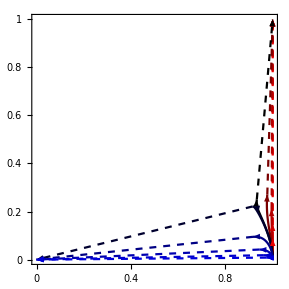

## Computing the probability of escape (Fig. 5A and S10A)

```mathematica
eqpoints[ss_,cc_,hh_,mm_]:=Module[{y1,out,qnext1,qnext2,q,sn,sc,q1,q2,outq2},(*Gives the equilibrium solutions for s,c,h,m*)
If[ss==0,out={{0,0},{1,1}},
qnext1=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q1+mm q2};(*Eq. 3*)
qnext2=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->(1-mm)q2+mm q1};(*Eq. 3*)
(*Next 4 code lines switch from Eq.3 to Eq. S2. Activate these lines for generating Fig. S10 (selection before migration)*)
(*qnext1a=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1- ss),q->q1};
qnext2b=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1- ss),q->q2};
qnext1=((1-aa mm)qnext1a+mm qnext2b)/(1-aa mm+mm);
qnext2=((1-mm )qnext2b+aa mm qnext1a)/(1+aa mm-mm);*)
eqSolutions=NSolve[qnext1==q1&&qnext2==q2,{q1,q2}];(*Finding equilibrium solutions for Eq. 3*)
eqSolutions2=N[Round[Table[{e⟦1,2⟧,e⟦2,2⟧},{e,eqSolutions}],10^-3]];
eqSolutions3=DeleteCases[Table[If[Im[e⟦1⟧]==0&&Im[e⟦2⟧]==0,e,Null],{e,eqSolutions2}],Null];(*Selects all the real equilibria*)
eqSolutions4=DeleteCases[Table[If[0≤e⟦1⟧≤1&&0≤e⟦2⟧≤1,e,Null],{e,eqSolutions3}],Null];(*Selects all the equilibria in the interval [0,1] *)
out=eqSolutions4
];
out
]

dynamics[q10_,q20_,s_,c_,h_,m_,time_]:=Module[{q1,q2,list1,list2,q1t,q2t},(*two lists of the dynamics, for q1 and q2, given starting conditions (q10,q20), for "time" generations*)
q1=q10;q2=q20;
list1={q1};list2={q2};
sn=1/2(1-c)(1-h s);
sc=(1-s)c;
Do[
q1mig=(1-m)q1+m q2;
q2mig=(1-m)q2+m q1;
meanfit1=q1mig^2(1-s)+2q1mig(1-q1mig)(2sn+sc)+(1-q1mig)^2;
meanfit2=q2mig^2(1-s)+2q2mig(1-q2mig)(2sn+sc)+(1-q2mig)^2;
q1t=(q1mig^2(1-s)+q1mig(1-q1mig)(sn+sc))/meanfit1;
q2t=(q2mig^2(1-s)+q2mig(1-q2mig)(sn+sc))/meanfit2;
(*Next 2 code lines switch from Eq.3 to Eq. S2. Activate these lines for generating Fig. S10 (selection before migration)*)
(*q1t=(1-m)*(q1^2(1-s)+q1(1-q1)(sn+2sc))/(q1^2(1-s)+2q1(1-q1)(sn+sc)+(1-q1)^2)+m*(q2^2(1-s)+q2(1-q2)(sn+2sc))/(q2^2(1-s)+2q2(1-q2)(sn+sc)+(1-q2)^2);
q2t=(1-m)*(q2^2(1-s)+q2(1-q2)(sn+2sc))/(q2^2(1-s)+2q2(1-q2)(sn+sc)+(1-q2)^2)+m*(q1^2(1-s)+q1(1-q1)(sn+2sc))/(q1^2(1-s)+2q1(1-q1)(sn+sc)+(1-q1)^2);*)
q1=q1t;q2=q2t;
AppendTo[list1,q1];
AppendTo[list2,q2];
,time];
{list1,list2}
]

attractor[q10_,q20_,s_,c_,h_,m_,time_,th_,attarctors_]:=Module[{dd,dd1,distances,a1},(*Given a list of attractors, for a point (q10,q20) returns the closest attractor after dynamics run of length "time", as long as it is within distance "th" in allele frequncy space (return the position of the attractor in the list of attractors). If there are no equilibra at distance "th", returns 0*)
dd=dynamics[q10,q20,s,c,h,m,time];
dd1={Last[dd⟦1⟧],Last[dd⟦2⟧]};
distances=Table[EuclideanDistance[dd1,a],{a,attarctors}];
a1=Position[distances,Min[distances]]⟦1,1⟧;
If[distances⟦a1⟧<th,a1,0]
]

traj[s_,c_,h_,m_,Ne_,time_,q0_]:=Module[{q1,q2,q1t,q2t,list},(*A simulated trajectory of length "time" starting at q0 with genetic drift Ne(Hapliod)*)
q1=q0⟦1⟧;q2=q0⟦2⟧;
list={{q1,q2}};
sc=c*(1-s); 
sn=1/2(1-c)*(1-h*s);
Do[
q1mig=(1-m)q1+m q2;
q2mig=(1-m)q2+m q1;
meanfit1=q1mig^2(1-s)+2q1mig(1-q1mig)(2sn+sc)+(1-q1mig)^2;
meanfit2=q2mig^2(1-s)+2q2mig(1-q2mig)(2sn+sc)+(1-q2mig)^2;
q1t=(q1mig^2(1-s)+q1mig(1-q1mig)(sn+sc))/meanfit1;
q2t=(q2mig^2(1-s)+q2mig(1-q2mig)(sn+sc))/meanfit2;
(*Next 2 code lines switch from Eq.3 to Eq. S2. Activate these lines for generating Fig. S10 (selection before migration)*)
(*q1t=(1-m)*(q1^2(1-s)+q1(1-q1)(sn+2sc))/(q1^2(1-s)+2q1(1-q1)(sn+sc)+(1-q1)^2)+m*(q2^2(1-s)+q2(1-q2)(sn+2sc))/(q2^2(1-s)+2q2(1-q2)(sn+sc)+(1-q2)^2);
q2t=(1-m)*(q2^2(1-s)+q2(1-q2)(sn+2sc))/(q2^2(1-s)+2q2(1-q2)(sn+sc)+(1-q2)^2)+m*(q1^2(1-s)+q1(1-q1)(sn+2sc))/(q1^2(1-s)+2q1(1-q1)(sn+sc)+(1-q1)^2);*)
q1t=N[1/Ne RandomInteger[BinomialDistribution[Ne,q1t]]];
q2t=N[1/Ne RandomInteger[BinomialDistribution[Ne,q2t]]];
q1=q1t;q2=q2t;
AppendTo[list,{q1,q2}];
,time];
list
]

AttractionBasins[s_,c_,h_,m_,th_,time_]:=Module[{eeeqs},(*Plots a 101*101 array for q1*q2 of attarction basins associated witheachpoint in allele freqeuncy space*)
eeeqs=N[eqpoints[s,c,h,m]];
txx=ParallelTable[attractor[q1,q2,s,c,h,m,time,th,eeeqs],{q1,0,1,0.01},{q2,0,1,0.01}]
]

trajQ[s_,c_,h_,m_,Ne_,time2_,ab_,dte_]:=Module[{traj,abasins},(*For the scenario parameters (s,c,h,m,Ne), a grid of associated attraction basins ab, and the DTE "dte", run a stochastic simulated trajectry and check whether the trajectry starting at the DTE escapes the basin of attraction of the DTE within "time2" generations*)
t1=traj[s,c,h,m,Ne,time2,dte];
t2=Round[100 t1]+1;
t3=Table[ab⟦t⟦1⟧,t⟦2⟧⟧,{t,t2}];(*A list of the attraction basins for each point in the trajectory*)
abasins=Union[t3];
If[Length[Union[t3]]==1,1,0] (*If at some point in the trajectory the frequencies are in a basin of attraction other then the DTE's, retun 0, otherwise return 1 *)
]

eq1[m_,s_,sc_,sn_]:=(((1-m)q1+m q2)^2(1-s)+((1-m)q1+m q2)(1-((1-m)q1+m q2))(sn+sc))/(((1-m)q1+m q2)^2(1-s)+2((1-m)q1+m q2)(1-((1-m)q1+m q2))(2sn+sc)+(1-((1-m)q1+m q2))^2);

eq2[m_,s_,sc_,sn_]:=(((1-m)q2+m q1)^2(1-s)+((1-m)q2+m q1)(1-((1-m)q2+m q1))(sn+sc))/(((1-m)q2+m q1)^2(1-s)+2((1-m)q2+m q1)(1-((1-m)q2+m q1))(2sn+sc)+(1-((1-m)q2+m q1))^2);
(*Next 2 code lines switch from Eq.3 to Eq. S2. Activate these lines for generating Fig. S10 (selection before migration)*)
(*eq1[m_,s_,sc_,sn_]:=(1-m)*(q1^2(1-s)+q1(1-q1)(sn+2sc))/(q1^2(1-s)+2q1(1-q1)(sn+sc)+(1-q1)^2)+m*(q2^2(1-s)+q2(1-q2)(sn+2sc))/(q2^2(1-s)+2q2(1-q2)(sn+sc)+(1-q2)^2)
eq2[m_,s_,sc_,sn_]:=(1-m)*(q2^2(1-s)+q2(1-q2)(sn+2sc))/(q2^2(1-s)+2q2(1-q2)(sn+sc)+(1-q2)^2)+m*(q1^2(1-s)+q1(1-q1)(sn+2sc))/(q1^2(1-s)+2q1(1-q1)(sn+sc)+(1-q1)^2)*)
Dq1[m_,s_,sc_,sn_]:=eq1[m,s,sc,sn]-q1;
Dq2[m_,s_,sc_,sn_]:=eq2[m,s,sc,sn]-q2;
J[m_,s_,sc_,sn_] := {{D[Dq1[m,s,sc,sn], q1],D[Dq1[m,s,sc,sn], q2]}, {D[Dq2[m,s,sc,sn], q1], D[Dq2[m,s,sc,sn], q2]}};

stableEigenVal[m_,s_,h_,c_]:=Module[{sn,sc,v1,eqPts,eigenVal,stableInd},
sc=c*(1-s); 
sn=1/2(1-c)*(1-h*s);
eqPts=Quiet[NSolve[{Dq1[m,s,sc,sn]==0, Dq2[m,s,sc,sn]==0},{q1,q2}, Reals]];
eqPts=Table[{e⟦1,1⟧->N[Round[e⟦1,2⟧,10^-5]],e⟦2,1⟧->N[Round[e⟦2,2⟧,10^-5]]},{e,eqPts}];
eigenVal=Eigenvalues[J[m,s,sc,sn]]/.eqPts;
stableInd=MapThread[And,{Negative[Re[eigenVal[[All,1]]]],  Negative[Re[eigenVal[[All,2]]]]}];
v1=Transpose[{Pick[eqPts,stableInd], Pick[eigenVal,stableInd]}];
Table[{{v⟦1,1,2⟧,v⟦1,2,2⟧},v⟦2⟧},{v,v1}]
]

ProbEscape[s_,c_,h_,m_,Ne_,th_,time1_,time2_,reps_]:=Module[{eqs,ab,ev,asb,aa,r1,prob},(*time1 = for constructing basins, time to allow for convergence; th= distance from equilibria where convergence is assumed; time2= length of trajectory from stable point;*)
eqs=eqpoints[s,c,h,m];
If[Length[eqs]≠9,prob="N1",
ab=AttractionBasins[s,c,h,m,th,time1];
If[MemberQ[Flatten[ab],0],Print["time1 too low ----- s=",s," c=",c," h=",h," m=",m ]];
ev=N[Round[stableEigenVal[m,s,h,c],10^-5]];
If[Length[ev]≠4,prob="N2",
asb=Select[ev,#⟦1,1⟧≠#⟦1,2⟧&];(*assymetric stable equilibria with their eigenvalues*)
asb=Flatten[Take[asb,All,1],1];(*assymetric stable equilibria *)
aa=asb[[1]];(*An assymetric stable point - the DTE*)
r1=ParallelTable[trajQ[s,c,h,m,Ne,time2,ab,aa],{reps}];
prob=N[1/reps Count[r1,0]]
];
];
prob
]
```

```mathematica
c=1;h=0;th=0.01;time1=200;Ne=100;time2=100;reps=1000;maxm=0.11;
```

```mathematica
res=Table[Table[{m,s,ProbEscape[s,c,h,m,Ne,th,time1,time2,reps]},{m,0,maxm,0.0005}],{s,0.5,1,0.005}];
```

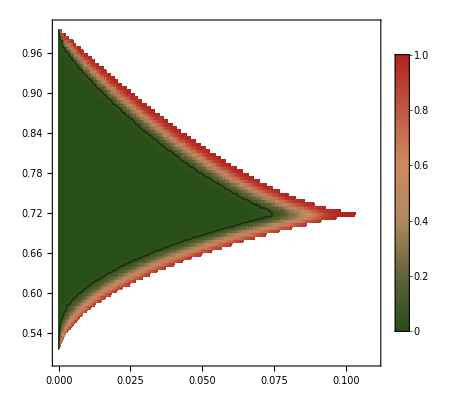

```mathematica
b0=ListDensityPlot[res,DataRange->{{0,maxm},{0.5,1}},PlotRange->{{0,maxm},{0.5,1}},PlotLegends->Automatic,ColorFunction->"RoseColors",FrameTicksStyle->Directive[Black,13]];
cfff[x_]:=Opacity[0,Blue]
b2=ListContourPlot[res,DataRange->{{0,maxm},{0.5,1}},PlotRange->{{0,maxm},{0.5,1}},ColorFunction->cfff,Contours->{0.05},ContourStyle->Directive[Black,Thick],ContourShading->True];
bbb=Show[b0,b2]
```

## Computing the stability radius (Fig. 5B and S10B)

```mathematica
SafetyRadius[s_,c_,h_,m_,th_,time1_]:=Module[{},
eqs=eqpoints[s,c,h,m];
If[Length[eqs]≠9,radius="N1",
ab=AttractionBasins[s,c,h,m,th,time1];
If[MemberQ[Flatten[ab],0],Print["time1 to low ----- s=",s," c=",c," h=",h," m=",m,"---",DateString[] ]];
ev=N[Round[stableEigenVal[m,s,h,c],10^-5]];
If[Length[ev]≠4,radius="N2",
asb=Select[ev,#⟦1,1⟧≠#⟦1,2⟧&];(*assmetric stable equilibria with their eigenvalues*)
asb=Flatten[Take[asb,All,1],1];(*assmetric stable equilibria *)
aa=asb[[1]];(*An assymetric stable point*)
id=ab⟦Round[100aa⟦1⟧]+1,Round[100aa⟦2⟧]+1⟧;
l1=0.01(Position[ab,id]-1);
l2=Complement[Flatten[Table[{i,j},{i,0,1,0.01},{j,0,1,0.01}],1],l1];
dist=Table[EuclideanDistance[aa,l],{l,l2}];
radius=Min[dist]
];
];
radius
]
```

```mathematica
c=1;h=0;th=0.01;time1=300;
maxm=0.11;
res=Table[Table[{m,s,SafetyRadius[s,c,h,m,th,time1]},{m,0,maxm,0.0005}],{s,0.5,1,0.005}]
```

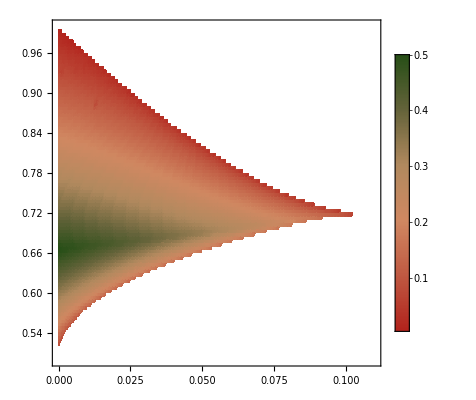

```mathematica
b0=ListDensityPlot[res,DataRange->{{0,maxm},{0.5,1}},PlotRange->{{0,0.11},{0.5,1}},PlotLegends->Automatic,ColorFunction->ColorData[{"RoseColors","Reverse"}],FrameTicksStyle->Directive[Black,13]]
```

## Computing m^* and q_2^* with asymmetric migration (Fig. 6, S12 & S13)

```mathematica
$HistoryLength=0;
DTEvalid[cc_,hh_,ss_,mm_,aa_]:=Module[{y1,y2,out,qnext1,qnext2,q,sn,sc,q1,q2,eqSolutions,eqSolutions2,outq2,rr2,rr3,rr4,rr5,rr6,jacobian},(*For a given c,h,s, and m, tests if there are 9 equilibrium solutions to Eq. 3, and returns also the Subscript[q, 2] of the DTE*)
out=1;outq2="Na";
If[mm aa>1,out=0;];
If[ss==0,out=0,
qnext1=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->((1-aa mm)q1+mm q2)/(1-aa mm+mm)};(*Eq. 3*)
qnext2=(q^2(1-ss)+2q(1-q)(sn+sc))/(q^2(1-ss)+2q(1-q)(2sn +sc)+(1-q)^2)/.{sn->1/2(1-cc)(1-hh ss),sc->cc(1-ss),q->((1-mm )q2+aa mm q1)/(1+aa mm-mm)};(*Eq. 3*)
eqSolutions=Quiet[NSolve[qnext1==q1&&qnext2==q2,{q1,q2}]];(*Finding equilibrium solutions for Eq. 3*)
eqSolutions2=N[Round[Table[{e⟦1,2⟧,e⟦2,2⟧},{e,eqSolutions}],10^-3]];
If[Union[Flatten[Table[{Im[e⟦1⟧],Im[e⟦2⟧]},{e,eqSolutions2}]]]≠{0},out=0];(*Checks that all solutions are real*)
y2=If[out==1,Union[Table[If[0≤t≤1,1,0],{t,Flatten[eqSolutions2]}]]];(*Checks that all solutions are between 0 and 1*)
If[y2≠{1},out=0];
If[out==1,(*Compute Subscript[q, 2] of the DTE*)
jacobian={{D[qnext1,q1],D[qnext1,q2]},{D[qnext2,q1],D[qnext2,q2]}}; (*The Jacobian from equation 5.*)
rr2=Table[Abs[Eigenvalues[jacobian/.{r⟦1⟧,r⟦2⟧}]],{r,eqSolutions}]; (*Taking the absolute eigenvalues for the jacobian evaluated at the different solutions*)
rr3=Table[If[e⟦1⟧<1&&e⟦2⟧<1,True,False],{e,rr2}];(*Testing to see for each equilibrium point if it is stable*)
rr4=Round[Table[{e⟦1,2⟧,e⟦2,2⟧},{e,eqSolutions}],0.00001];
rr5=Table[If[rr3⟦i⟧&&(rr4⟦i,1⟧>rr4⟦i,2⟧),rr4⟦i,2⟧,Null],{i,Length[eqSolutions]}]; (*Taking all the points that are stable and Subscript[q, 1]>Subscript[q, 2]*)
rr6=DeleteCases[rr5,Null];
If[rr6=={},out=0];(*If there are no DTEs, out=0*)
outq2=If[Length[rr6]==1,rr6⟦1⟧,Null] (*Making sure that there is only one DTE, and taking Subscript[q, 2] of the DTE*)
];
];
{out,outq2}(*out=1 means DTE exists, otherwise out=0*)
]

mqstar[cc_,hh_,ss_,aa_]:=Module[{maxm,jumps,t0,t1,t2,t3,outm,w1,outq}, (*For a given c, h, and s, returns m^* and Subscript[q, 2]^* *)
If[DTEvalid[cc,hh,ss,0]⟦1⟧==0,outm="Na";outq="Na",
maxm=0.2;(*Maximal m for searching m^* *)
jumps=10^-3;(*Resolution in m for searching m^*  *)
t0=Table[{N[mm],DTEvalid[cc,hh,ss,mm,aa]},{mm,0,maxm,jumps}];
t1=Table[{t⟦1⟧,t⟦2,1⟧},{t,t0}];
t2=Flatten[Take[t1,All,{2}]];
t3=Flatten[t1⟦FirstPosition[t2,0]-1⟧]⟦1⟧;
outm=If[NumberQ[t3],t3,"Na"];
w1=Table[{t⟦1⟧,t⟦2,2⟧},{t,t0}];
outq=Max[DeleteCases[Flatten[Take[w1,All,{2}]],"Na"]]
];
{outm,outq}
]

ComputeGridmqstar[h_,aa_]:=Module[{jmps,jmpc,ress,pmstar,pqstar},
jmps=0.01;(*resolution in s*)
jmpc=0.01;(*resolution in c*)
ress=Quiet[ParallelTable[Table[{ccc,sss,mqstar[ccc,h,sss,aa]},{ccc,0,1,jmpc}],{sss,0,1,jmps}]];
pmstar=Table[{r⟦1⟧,r⟦2⟧,r⟦3,1⟧},{r,Flatten[ress,1]}];
pqstar=Table[{r⟦1⟧,r⟦2⟧,r⟦3,2⟧},{r,Flatten[ress,1]}];
{pmstar,pqstar}
]
```

```mathematica
h=1;
a=10;
p1=ComputeGridmqstar[h,a];
```

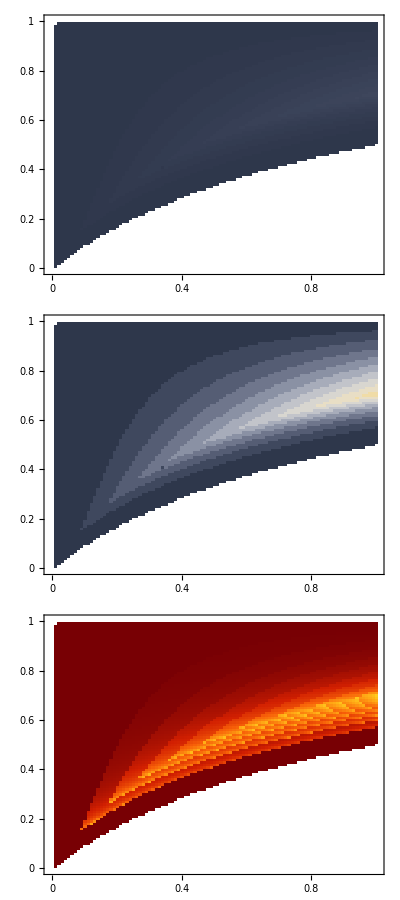

```mathematica
cf1[x_]:=If[!NumberQ[x],White,ColorData["GrayYellowTones"][x/0.107]]
cf2[x_]:=If[!NumberQ[x],White,ColorData["SolarColors"][x/0.28]]
si=210;
nn=Sqrt[Dimensions[p1[[1]]][[1]]];
mm1=Partition[Flatten[Take[p1⟦1⟧,All,{3}]],nn];
mmx1=Table[Table[If[NumberQ[mm1⟦i,j⟧],10mm1⟦i,j⟧,mm1⟦i,j⟧],{j,Length[mm1]}],{i,Length[mm1]}];
mmq1=Partition[Flatten[Take[p1⟦2⟧,All,{3}]],nn];
ticks={0,0.2,0.4,0.6,0.8,1};
ticksize=15;
gmm1=MatrixPlot[Reverse[mm1],ColorFunction->cf1,ColorFunctionScaling->False,DataRange->{{0,1},{0,1}},FrameLabel->None,FrameTicks->ticks,FrameTicksStyle->ticksize,ImageSize->si];
gmmx1=MatrixPlot[Reverse[mmx1],ColorFunction->cf1,ColorFunctionScaling->False,DataRange->{{0,1},{0,1}},FrameLabel->None,FrameTicks->ticks,FrameTicksStyle->ticksize,ImageSize->si];
gmmq1=MatrixPlot[Reverse[mmq1],ColorFunction->cf2,ColorFunctionScaling->False,DataRange->{{0,1},{0,1}},FrameLabel->None,FrameTicks->ticks,FrameTicksStyle->ticksize,ImageSize->si];
ggg=Grid[{{gmm1},{gmmx1},{gmmq1}}]
```

## Computing number of solutions (Figs. S3-S9)

```mathematica
eq1[m_,s_,sc_,sn_]:=(((1-m)q1+m q2)^2(1-s)+((1-m)q1+m q2)(1-((1-m)q1+m q2))(sn+2sc))/(((1-m)q1+m q2)^2(1-s)+2((1-m)q1+m q2)(1-((1-m)q1+m q2))(sn+sc)+(1-((1-m)q1+m q2))^2);

eq2[m_,s_,sc_,sn_]:=(((1-m)q2+m q1)^2(1-s)+((1-m)q2+m q1)(1-((1-m)q2+m q1))(sn+2sc))/(((1-m)q2+m q1)^2(1-s)+2((1-m)q2+m q1)(1-((1-m)q2+m q1))(sn+sc)+(1-((1-m)q2+m q1))^2);
(*For selection-before-migration model (Eq.S2, Figs. S7-S9), use th equations in the next two code lines instead of the pvious two lines*)
(*eq1[m_,s_,sc_,sn_]:=(1-m)*(q1^2(1-s)+q1(1-q1)(sn+2sc))/(q1^2(1-s)+2q1(1-q1)(sn+sc)+(1-q1)^2)+m*(q2^2(1-s)+q2(1-q2)(sn+2sc))/(q2^2(1-s)+2q2(1-q2)(sn+sc)+(1-q2)^2)
eq2[m_,s_,sc_,sn_]:=(1-m)*(q2^2(1-s)+q2(1-q2)(sn+2sc))/(q2^2(1-s)+2q2(1-q2)(sn+sc)+(1-q2)^2)+m*(q1^2(1-s)+q1(1-q1)(sn+2sc))/(q1^2(1-s)+2q1(1-q1)(sn+sc)+(1-q1)^2)*)
Dq1[m_,s_,sc_,sn_]:=eq1[m,s,sc,sn]-q1;
Dq2[m_,s_,sc_,sn_]:=eq2[m,s,sc,sn]-q2;
J[m_,s_,sc_,sn_] := {{D[Dq1[m,s,sc,sn], q1],D[Dq1[m,s,sc,sn], q2]}, {D[Dq2[m,s,sc,sn], q1], D[Dq2[m,s,sc,sn], q2]}};

stableEigenVal[m_,s_,h_,c_]:=Module[{sn,sc,v1,eqPts,eigenVal,stableInd},
sc=c*(1-s); 
sn=(1-c)*(1-h*s);
eqPts=Quiet[NSolve[{Dq1[m,s,sc,sn]==0, Dq2[m,s,sc,sn]==0},{q1,q2}, Reals]];
eqPts=Table[{e⟦1,1⟧->N[Round[e⟦1,2⟧,10^-5]],e⟦2,1⟧->N[Round[e⟦2,2⟧,10^-5]]},{e,eqPts}];
eigenVal=Eigenvalues[J[m,s,sc,sn]]/.eqPts;
stableInd=MapThread[And,{Negative[Re[eigenVal[[All,1]]]],  Negative[Re[eigenVal[[All,2]]]]}];
v1=Transpose[{Pick[eqPts,stableInd], Pick[eigenVal,stableInd]}];
Table[{{v⟦1,1,2⟧,v⟦1,2,2⟧},v⟦2⟧},{v,v1}]
]

StabilityRadius[m_,s_,h_,c_]:=Module[{},
r1=stableEigenVal[m,s,h,c];
r2=Table[{{r⟦1,1,2⟧,r⟦1,2,2⟧},Min[Abs[r⟦2⟧]]},{r,r1}];
r3=N[Round[r2,10^-8]];
r4=Select[r3,#⟦1⟧=={0.,0.}||#⟦1⟧=={1.,1.}&];
r5=Complement[r3,r4];
If[Length[r5]==2&&r5⟦1,2⟧==r5⟦1,2⟧,sr=r5⟦1,2⟧,Print["Error"]];
sr
]


cff2[x_]:=Which[x==7,Lighter[Blue,0.3],x==5,Lighter[Blue,0.6],x==3,Lighter[Blue,0.9],!IntegerQ[x],Lighter[Red,0.8(1-x)],True,White];
(*Color function for the stability grid*)

stabilitygrid[h_,m_]:=Module[{kk,qq1,qq2},
kk=ParallelTable[Table[If[Length[eqpoints[s,c,h,m]]≠9,Length[eqpoints[s,c,h,m]],StabilityRadius[m,s,h,c]],{c,0,1,0.01}],{s,0,1,0.01}];
qq1=ListPlot[{{0,1}},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->{{0,0.5,1},{0,0.5,1}},AspectRatio->1];
qq2=MatrixPlot[kk,DataReversed->True,FrameTicks->True,ColorFunctionScaling->False,ColorFunction->cff2,DataRange->{{0,1},{0,1}}];
Show[qq1,qq2]
]

cff3[x_]:=Which[
x==1,RGBColor["#00b359"],(*Green*)
x==2,RGBColor["#33d6ff"],(*Blue*)
x==3,RGBColor["#ff0066"],(*Red*)
x==4,RGBColor["#990099"],(*Purple*)
x==5,RGBColor["#ff7733"],(*Orange*)
x==6,White,
True,White];
(*Color function for the stability grid*)

stabilitygrid2[h_,m_]:=Module[{qq1,qq2},
jumps=0.01;
kk=ParallelTable[Table[Neq=Length[eqpoints[s,c,h,m]];Nst=Length[stableEigenVal[m,s,h,c]];Which[
Neq==9&&Nst==4,1,(*9 eq points; 2 assymetric stable*)
Neq==5(*&&Nst==2*),2,(*5 eq points; 0 assymetric stable*)
Neq==3&&Nst==2,3,(*3 eq points; 0 assymetric stable, 1 symetric unstable*)
Neq==9&&Nst==1,4,(*9 eq points; 0 assymetric stable*)
Neq==3&&Nst==1,5,(*3 eq points; 0 assymetric stable, 1 symetric stable*)
Neq==2&&Nst==1,6,(*2 eq points; 1 stable*)
Neq==2&&Nst==2,6,(*2 eq points; 2 stable*)
True,7],
{c,0,1,jumps}],{s,0,1,jumps}];
qq1=ListPlot[{{0,1}},PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->{{0,0.5,1},{0,0.5,1}},AspectRatio->1];
qq2=MatrixPlot[kk,DataReversed->True,FrameTicks->True,ColorFunctionScaling->False,ColorFunction->cff3,DataRange->{{0,1},{0,1}}];
Show[qq1,qq2]
]
```

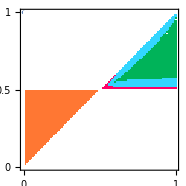

```mathematica
h=0;m=0.01;
DateString[]
stabilitygrid2[h,m]
DateString[]
```